```mathematica
f[x_]:=1/(2+2 *x+x^2);
l[n_]:=Array[-5+10/n*#&,n+1,0];
c[n_]:=Array[-5Cos[(2*#+1)/(2n+2)*Pi]&,n+1,0];
```

```mathematica
Subscript[X, 4]=l[4];
Subscript[X, 8]=l[8];
Subscript[X, 16]=l[16];
Subscript[L, 4] = Expand[InterpolatingPolynomial[Transpose[{Subscript[X, 4],f[Subscript[X, 4]]}],x]];
Subscript[L, 8] = Expand[InterpolatingPolynomial[Transpose[{Subscript[X, 8],f[Subscript[X, 8]]}],x]];
Subscript[L, 16] = Expand[InterpolatingPolynomial[Transpose[{Subscript[X, 16],f[Subscript[X, 16]]}],x]];
Plot[{Callout[f[x],"f(x)",Above,LabelStyle->Directive[Bold],Background->None,Appearance->"CurvedLeader"],Callout[Subscript[L, 4],"L_4(x)",{-1,0.2},-1,LabelStyle->Directive[Bold],Background->None,Appearance->"CurvedLeader"]},{x,-5,5},Filling->{1->{2}},AxesLabel->Automatic,PlotRange->Full]
Plot[{Callout[f[x],"f(x)",Above,LabelStyle->Directive[Bold],Background->None,Appearance->"CurvedLeader"],Callout[Subscript[L, 8],"L_8(x)",{-3,1.0},-4,LabelStyle->Directive[Bold],Background->None,Appearance->"CurvedLeader"]},{x,-5,5},Filling->{1->{2}},AxesLabel->Automatic,PlotRange->Full]
Plot[{Callout[f[x],"f(x)",{4,1},4.1,LabelStyle->Directive[Bold],Background->None,Appearance->"CurvedLeader"],Callout[Subscript[L, 16],"L_16(x)",{3,3},4.5,LabelStyle->Directive[Bold],Background->None,Appearance->"CurvedLeader"]},{x,-5,5},Filling->{1->{2}},AxesLabel->Automatic,PlotRange->Full]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Subscript[X, 4]=c[4];
Subscript[X, 8]=c[8];
Subscript[X, 16]=c[16];
Subscript[L, 4] = InterpolatingPolynomial[Transpose[{Subscript[X, 4],f[Subscript[X, 4]]}],x];
Subscript[L, 8] = InterpolatingPolynomial[Transpose[{Subscript[X, 8],f[Subscript[X, 8]]}],x];
Subscript[L, 16] = InterpolatingPolynomial[Transpose[{Subscript[X, 16],f[Subscript[X, 16]]}],x];
Plot[{Callout[f[x],"f(x)",Above,LabelStyle->Directive[Bold],Background->None,Appearance->"CurvedLeader"],Callout[Subscript[L, 4],"L_4(x)",{3.2,0.8},2,LabelStyle->Directive[Bold],Background->None,Appearance->"CurvedLeader"]},{x,-5,5},Filling->{1->{2}},AxesLabel->Automatic,PlotRange->Full]
Plot[{Callout[f[x],"f(x)",Above,LabelStyle->Directive[Bold],Background->None,Appearance->"CurvedLeader"],Callout[Subscript[L, 8],"L_8(x)",{-3,0.5},-3,LabelStyle->Directive[Bold],Background->None,Appearance->"CurvedLeader"]},{x,-5,5},Filling->{1->{2}},AxesLabel->Automatic,PlotRange->Full]
```

-Graphics-

-Graphics-

```mathematica
Plot[{Callout[f[x],"f(x)",{4,0.3},2.2,LabelStyle->Directive[Bold],Background->None,Appearance->"CurvedLeader"],Callout[Subscript[L, 16],"L_16(x)",{2.5,0.8},1.4,LabelStyle->Directive[Bold],Background->None,Appearance->"CurvedLeader"]},{x,-5,5},Filling->{1->{2}},AxesLabel->Automatic,PlotRange->Full]
```

-Graphics-

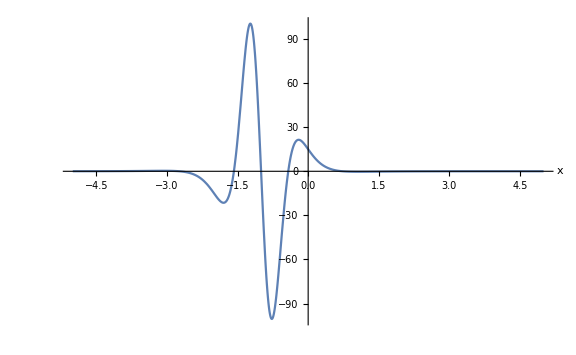
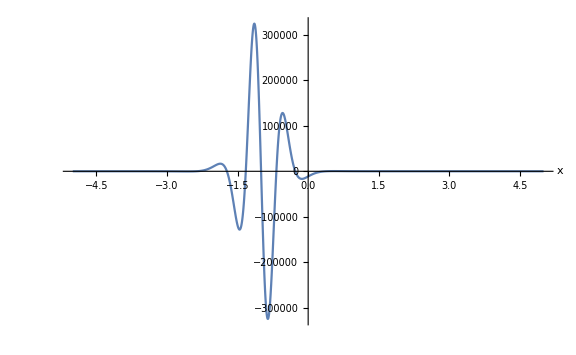
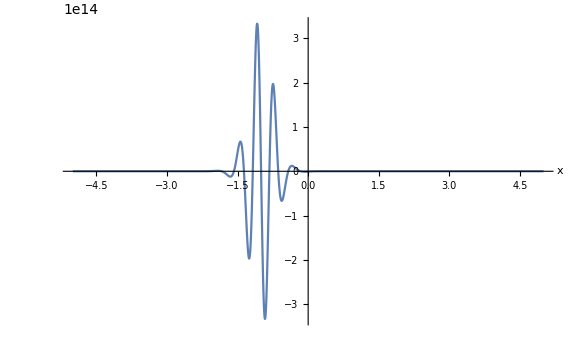

```mathematica
Table[Show[Plot[A,{x,-5,5},AxesLabel->Automatic,PlotRange->Full],ImageSize->Large],{A,Table[D[f[x],{x,n+1}],{n,{4,8,16}}]}]
```

```mathematica
Table[N[MaxValue[{Abs[D[f[x],{x,n+1}]],-5<=x≤5},x],13]/((n+1)!)*((5^(n+1))/(2^n)),{n,{4,8,16}}]
```

{163.5074592041,6817.348655088,1.090883874366×10^7}